```mathematica
f[x_]:=(x^3+2*x^2+15*x+2)*Sin[π*x];
f[0]
f[1]
FindRoot[f'[c]==0,{c,.5}]
```

0

0

{c→0.640241}

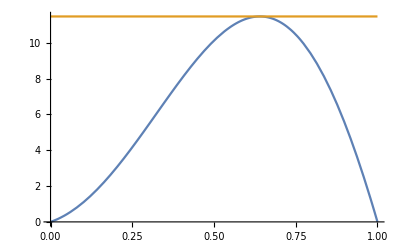

```mathematica
Plot[{f[x],f[.640241]},{x,0,1}]
```